## Inicializaciones

```mathematica
sizeP=11;
```

```mathematica
sizeC=2;
```

```mathematica
θA=π/2.;
```

```mathematica
θBplus=π/4.;
```

```mathematica
θBminus= -π/8.;
```

## Definiciones

### Funciones externas

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Espacios de Hilbert

```mathematica
baseP=IdentityMatrix[sizeP];
```

```mathematica
baseC=IdentityMatrix[sizeC];
```

### Funciones bra y ket

```mathematica
bra[c_,p_]:=KroneckerProduct[{baseC[[c+1]]},{baseP[[p+1+(sizeP-1)/2]]}]
```

```mathematica
ket[c_,p_]:=ConjugateTranspose[bra[c,p]]
```

```mathematica
braP[p_]:={baseP[[p+1+(sizeP-1)/2]]}
```

```mathematica
braC[c_]:={baseC[[c+1]]}
```

```mathematica
ketP[p_]:=braP[p]†
```

```mathematica
ketC[c_]:=braC[c]†
```

### Operadores

```mathematica
MatrixExp[-ⅈ  θ  PauliMatrix[2]/2]
```

{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

```mathematica
coinA=KroneckerProduct[{{Cos[θA/2],-Sin[θA/2]},{Sin[θA/2],Cos[θA/2]}},baseP];
```

```mathematica
θB[x_]:=(θBplus(1+Tanh[x])+θBminus(1-Tanh[x]))/2
```

```mathematica
coinB=Sum[
KroneckerProduct[{{Cos[θB[x]/2],-Sin[θB[x]/2]},{Sin[θB[x]/2],Cos[θB[x]/2]}},ketP[x].braP[x]],
{x,-(sizeP-1)/2, (sizeP-1)/2}
];
```

```mathematica
(* S = \sum_i |0, i+1\rangle\langle 0, i|  + \sum_i |1, i-1\rangle\langle 1, i| *)
```

```mathematica
shift=Sum[ket[0,i+1].bra[0,i],{i,-(sizeP-1)/2,(sizeP-1)/2-1}]+Sum[ket[1,i-1].bra[1,i],{i,-(sizeP-1)/2+1,(sizeP-1)/2}];
```

```mathematica
unitary[m_Integer,n_Integer]:=shift.Dot@@Join[Table[coinA,m],Table[coinB,n]]
```

### Caminatas

```mathematica
DTQW[state_,step_Integer,m_Integer,n_Integer]:=Nest[unitary[n,m].#&,N[state],step]
```

## Pruebas

```mathematica
state0=ket[1,0];
```

#### Losing strategies

```mathematica
lqw1=#.#†&@DTQW[state0,5,1,0];
```

```mathematica
lqw2=#.#†&@DTQW[state0,5,0,1];
```

```mathematica
probslqw1=Abs@Diagonal@MatrixPartialTrace[lqw1,1,{sizeC,sizeP}];
```

```mathematica
probslqw2=Abs@Diagonal@MatrixPartialTrace[lqw2,1,{sizeC,sizeP}];
```

```mathematica
Total@probslqw1
```

1.

```mathematica
Total@probslqw2
```

1.

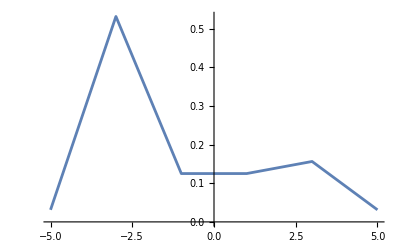

```mathematica
plotlqw1=ListLinePlot[{Range[-5,5,2],probslqw1[[;;;;2]]}ᵀ,PlotRange->All]
```

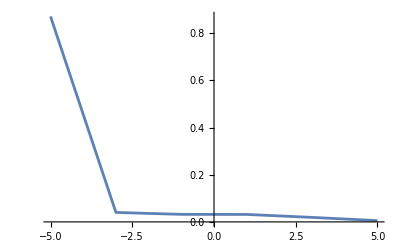

```mathematica
plotlqw2=ListLinePlot[{Range[-5,5,2],probslqw2[[;;;;2]]}ᵀ,PlotRange->All]
```

#### Winning strategies

```mathematica
wqw1=#.#†&@DTQW[state0,5,2,1];
```

```mathematica
wqw2=#.#†&@DTQW[state0,5,2,2];
```

```mathematica
probswqw1=Abs@Diagonal@MatrixPartialTrace[wqw1,1,{sizeC,sizeP}];
```

```mathematica
probswqw2=Abs@Diagonal@MatrixPartialTrace[wqw2,1,{sizeC,sizeP}];
```

```mathematica
Total@probswqw1
```

1.

```mathematica
Total@probswqw2
```

1.

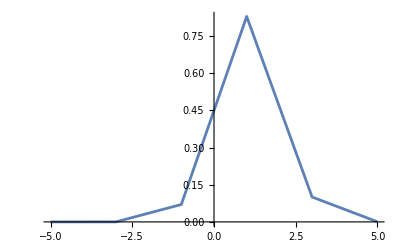

```mathematica
plotwqw1=ListLinePlot[{Range[-5,5,2],probswqw1[[;;;;2]]}ᵀ,PlotRange->All]
```

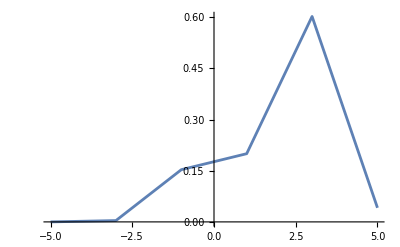

```mathematica
plotwqw2=ListLinePlot[{Range[-5,5,2],probswqw2[[;;;;2]]}ᵀ,PlotRange->All]
```